Helper tools

```mathematica
ClearAll["Global`*"]
basepath="/Users/basavyr/Documents/Work/Repos/mathematica-useful-algorithms/Physics/Elliptic-Functions-New-Boson/Figures/Frequencies";
export[object_,name_,format_]:=Export[StringTemplate["``/``.``"][basepath,name,format],object, ImageResolution->1500];
linspace[a_,b_,n_]:=Table[N[q],{q,a,b,(b-a)/(n-1)}];
```

Numerical values

```mathematica
MOIfit1={91,9,51};
MOIfit2={13.53,101.76,52.94};
MOIfit3={89,12,48};
thetadegfit1=-119;
thetadegfit2=140;
thetadegfit3=-71;
oddspin=5.5;
Ak[mois_]:=N[1/(2*#)]&/@mois;
rad[thetadeg_]:=N[thetadeg*π/180];
j1[thetadeg_]:=oddspin*Cos[rad[thetadeg]];
j2[thetadeg_]:=oddspin*Sin[rad[thetadeg]];
```

Analytical Formulas

```mathematica
A[I_,thetadeg_,mois_]:=Ak[mois][[2]](1-j2[thetadeg]/I)-Ak[mois][[1]];
u[I_,thetadeg_,mois_]:=(Ak[mois][[3]]-Ak[mois][[1]])/A[I,thetadeg,mois];
v0[I_,thetadeg_,mois_]:=-(Ak[mois][[1]]*j1[thetadeg])/A[I,thetadeg,mois];
```

## The wobbling frequency evaluated for 135Pr

Omega ω

```mathematica
A21[I_,thetadeg_,mois_]:=(Ak[mois][[2]]-Ak[mois][[1]]-(Ak[mois][[2]]*j2[thetadeg])/I);
omega[I_,thetadeg_,mois_]:=(((2I+1)*A21[I,thetadeg,mois]+2*Ak[mois][[1]]*j1[thetadeg])*((2I+1)*(Ak[mois][[3]]-Ak[mois][[1]])+2*Ak[mois][[1]]*j1[thetadeg])-(Ak[mois][[3]]-Ak[mois][[1]])*A21[I,thetadeg,mois])^(1/2);
```

Numerical values (tabulated

```mathematica
spinvalues=Table[spin,{spin,7.5,41.5,2}];
omegavaluesfit1=Table[{omega[spin,thetadegfit1,MOIfit1],omega[spin,thetadegfit1+180,MOIfit1]},{spin,spinvalues}];
omegavaluesfit2=Table[{omega[spin,thetadegfit2,MOIfit2],omega[spin,thetadegfit2+180,MOIfit2]},{spin,spinvalues}];
omegavaluesfit3=Table[{omega[spin,thetadegfit3,MOIfit3],omega[spin,thetadegfit3+180,MOIfit3]},{spin,spinvalues}];
numericalvalues=Table[{spinvalues[[i]],omegavaluesfit1[[i,1]],omegavaluesfit1[[i,2]],omegavaluesfit2[[i,1]],omegavaluesfit2[[i,2]],omegavaluesfit3[[i,1]],omegavaluesfit3[[i,2]]},{i,1,Length[spinvalues]}];
header={"I","ω1","ω1'","ω2","ω2'","ω3","ω3'"};
numericalvalues=Insert[numericalvalues,header,1];
```

```mathematica
Grid[numericalvalues,Frame->All]
```

I | ω1 | ω1' | ω2 | ω2' | ω3 | ω3'
7.5 | 0.229851 | 0.159683 | 0.803892 | 0.142569 | 0.319873 | 0.0729018
9.5 | 0.294886 | 0.232257 | 0.922509 | 0.262878 | 0.37244 | 0.136003
11.5 | 0.357647 | 0.298689 | 1.04118 | 0.382287 | 0.425068 | 0.193021
13.5 | 0.419196 | 0.36242 | 1.15989 | 0.501416 | 0.477717 | 0.248146
15.5 | 0.480018 | 0.424686 | 1.27861 | 0.620417 | 0.530372 | 0.3024
17.5 | 0.540366 | 0.48606 | 1.39734 | 0.739349 | 0.583027 | 0.356175
19.5 | 0.600387 | 0.546848 | 1.51608 | 0.858237 | 0.635679 | 0.409655
21.5 | 0.660174 | 0.607228 | 1.63482 | 0.977096 | 0.688329 | 0.462941
23.5 | 0.719786 | 0.667313 | 1.75357 | 1.09594 | 0.740975 | 0.516092
25.5 | 0.779264 | 0.727176 | 1.87232 | 1.21476 | 0.793618 | 0.569144
27.5 | 0.838637 | 0.78687 | 1.99107 | 1.33357 | 0.846258 | 0.622123
29.5 | 0.897927 | 0.84643 | 2.10982 | 1.45238 | 0.898896 | 0.675045
31.5 | 0.957149 | 0.905883 | 2.22857 | 1.57118 | 0.951531 | 0.727924
33.5 | 1.01632 | 0.965249 | 2.34733 | 1.68997 | 1.00416 | 0.780766
35.5 | 1.07544 | 1.02454 | 2.46608 | 1.80876 | 1.05679 | 0.83358
37.5 | 1.13452 | 1.08378 | 2.58484 | 1.92755 | 1.10942 | 0.88637
39.5 | 1.19357 | 1.14296 | 2.70359 | 2.04633 | 1.16205 | 0.93914
41.5 | 1.25259 | 1.2021 | 2.82235 | 2.16511 | 1.21468 | 0.991893

Graphical representations for ω

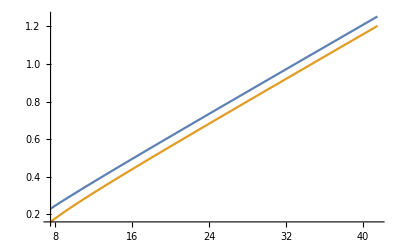

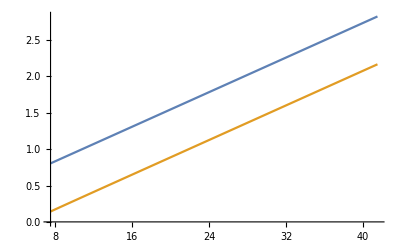

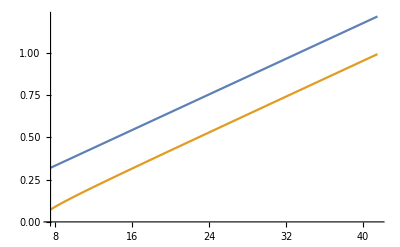

```mathematica
Plot[{omega[x,thetadegfit1,MOIfit1],omega[x,thetadegfit1+180,MOIfit1]},{x,7.5,41.5}]
Plot[{omega[x,thetadegfit2,MOIfit2],omega[x,thetadegfit2+180,MOIfit2]},{x,7.5,41.5}]
Plot[{omega[x,thetadegfit3,MOIfit3],omega[x,thetadegfit3+180,MOIfit3]},{x,7.5,41.5}]
```